```mathematica
x1=-6.0017;
x2=1.9983;
x3=1;
a0=0;
a1=1;
a2=1;
a3=4.0034;
A=Table[0,{x,4},{y,4}];
A[[1,1]]=-2*a0*x3;
A[[1,2]]=0;
A[[1,3]]=a0*x1+a1*x3;
A[[1,4]]=a0*x2-a2*x3;
A[[2,1]]=0;
A[[2,2]]=-2*a0*x3;
A[[2,3]]=a0*x2+a2*x3;
A[[2,4]]=-a0*x1+a1*x3;
A[[3,1]]=a0*x1+a1*x3;
A[[3,2]]=a0*x2+a2*x3;
A[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A[[3,4]]=a2*x1-a1*x2;
A[[4,1]]=a0*x2-a2*x3;
A[[4,2]]=-a0*x1+a1*x3;
A[[4,3]]=a2*x1-a1*x2;
A[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A
```

{{0,0,1.,-1.},{0,0,1.,1.},{1.,1.,6.0051,-8.},{-1.,1.,-8.,-2.0017}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

0

0.

0.

2

2

-16.

4.0034

2.0017

```mathematica
l1=0;
l2=1;
l3=-2;
a0=1;
a1=2.9997;
a2=-2;
B=Table[0,{x,4},{y,4}];
B[[1,1]]=0;
B[[1,2]]=0;
B[[1,3]]=a0*l1;
B[[1,4]]=a0*l2;
B[[2,1]]=0;
B[[2,2]]=0;
B[[2,3]]=a0*l2;
B[[2,4]]=-a0*l1;
B[[3,1]]=a0*l1;
B[[3,2]]=a0*l2;
B[[3,3]]=-(a1*l1+a2*l2)+a0*l3;
B[[3,4]]=(a2*l1-a1*l2);
B[[4,1]]=a0*l2;
B[[4,2]]=-a0*l1;
B[[4,3]]=(a2*l1-a1*l2);
B[[4,4]]=(a1*l1+a2*l2)+a0*l3;
B
```

{{0,0,0,1},{0,0,1,0},{0,1,0.,-2.9997},{1,0,-2.9997,-4.}}

```mathematica
q1=0
q2=2*a0*l1
q3=2*a0*l2
q4=0
q5=0
q6=-2*a1*l2+2*a2*l1
q7=-a1*l1-a2*l2
q8=a0*l3
```

0

0

2

0

0

-5.9994

2.

-2

```mathematica
myplot=ContourPlot3D[{A[[1, 1]]*x^2 + (A[[1, 2]] + A[[2, 1]])*x*y + (A[[1, 3]] + A[[3, 1]])*x*z + (A[[1, 4]] + A[[4, 1]])*x + A[[2, 2]]*y^2 + (A[[2, 3]] + A[[3, 2]])*y*z + (A[[2, 4]] + A[[4, 2]])*y + A[[3, 3]]*z^2 + (A[[3, 4]] + A[[4, 3]])*z + A[[4, 4]] == 0, B[[1, 1]]*x^2 + (B[[1, 2]] + B[[2, 1]])*x*y + (B[[1, 3]] + B[[3, 1]])*x*z + (B[[1, 4]] + B[[4, 1]])*x + B[[2, 2]]*y^2 + (B[[2, 3]] + B[[3, 2]])*y*z + (B[[2, 4]] + B[[4, 2]])*y + B[[3, 3]]*z^2 + (B[[3, 4]] + B[[4, 3]])*z + B[[4, 4]] == 0}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, PerformanceGoal -> "Quality", MeshStyle -> Gray, Mesh -> 0, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}, MaxRecursion -> 15, PlotPoints -> 50, PlotRange -> Automatic, ContourStyle -> {{Orange, Opacity[0.5]}, {Magenta,Opacity[0.5]}}];
Show[myplot]
```

-Graphics3D-

```mathematica
eigenvalues=Eigenvalues[A];
eigenvectors=Eigenvectors[A];
transformatrix=Transpose[{eigenvectors[[1]],eigenvectors[[3]],eigenvectors[[2]], eigenvectors[[4]]}];
```

```mathematica
afterA=Transpose[transformatrix].A.transformatrix;
MatrixForm[afterA]
```

(11.1272 | 1.55431×10^-15 | 1.77636×10^-15 | -7.21645×10^-16
1.56125×10^-15 | 0.276968 | 4.05231×10^-15 | 5.92321×10^-15
1.77636×10^-15 | 3.88578×10^-15 | -7.22106 | -1.16573×10^-15
-6.69603×10^-16 | 5.92538×10^-15 | -1.22298×10^-15 | -0.179739)

```mathematica
afterB=Transpose[transformatrix].B.transformatrix;
MatrixForm[afterB]
```

(1.47349 | 1.03172 | 0.370817 | 0.503178
1.03172 | -0.0868625 | -0.75943 | -0.0526926
0.370817 | -0.75943 | -5.49073 | -0.891463
0.503178 | -0.0526926 | -0.891463 | 0.104101)

```mathematica
Clear[V];Clear[u];Clear[v];
V={(u+afterA[[1,1]]*v)/afterA[[1,1]], (u*v-afterA[[2,2]])/afterA[[2,2]], (u-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
goalformula=Collect[Expand[V.afterB.V], {u^2, u}]
```

0.204371+0.0477441 v-7.90803 v^2+u^2 (-0.0489986-0.428353 v-0.746543 v^2)+u (-0.150636+3.5712 v+28.6875 v^2)

```mathematica
delta=Expand[(-0.1506359501567861+3.571197030636359 v+28.687476209290608 v^2)^2-4*(-0.048998606422499424-0.4283534362250473 v-0.7465426027860118 v^2)*(0.20437103712993776+0.04774411179488669 v-7.908028206596708 v^2)];
```

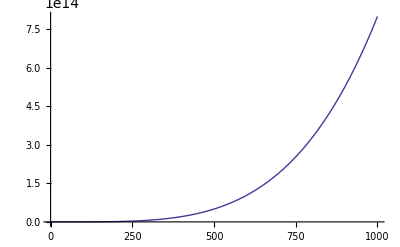

```mathematica
Plot[delta, {v,-0.2, 1000}]
```

```mathematica
Solve[delta==0, v]
```

{{v→-0.157769},{v→-0.157769},{v→0.0379911-0.0413557 ⅈ},{v→0.0379911+0.0413557 ⅈ}}

```mathematica
u1=(-(-0.1506359501567861+3.571197030636359 v+28.687476209290608 v^2)+Sqrt[delta])/(2*(-0.048998606422499424-0.4283534362250473 v-0.7465426027860118 v^2));
u2=(-(-0.1506359501567861+3.571197030636359 v+28.687476209290608 v^2)-Sqrt[delta])/(2*(-0.048998606422499424-0.4283534362250473 v-0.7465426027860118 v^2));
```

```mathematica
afterP1={(u1+afterA[[1,1]]*v)/afterA[[1,1]], (u1*v-afterA[[2,2]])/afterA[[2,2]], (u1-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u1*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
afterP2={(u2+afterA[[1,1]]*v)/afterA[[1,1]], (u2*v-afterA[[2,2]])/afterA[[2,2]], (u2-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u2*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
P1=transformatrix.afterP1;
P2=transformatrix.afterP2;
```

```mathematica
Branch11=Graphics3D[{PointSize[0.01],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,-60, -0.27, 0.001}]]},Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}];
Branch111=Graphics3D[{PointSize[0.01],Black,Point[Table[{P1[[1]]/P1[[4]],P1[[2]]/P1[[4]],P1[[3]]/P1[[4]]},{v,-0.06, 50, 0.001}]]}];
Branch12=Graphics3D[{PointSize[0.01],Black,Point[Table[{P2[[1]]/P2[[4]],P2[[2]]/P2[[4]],P2[[3]]/P2[[4]]},{v,-0.058,0.055, 0.0001}]]}];
Show[Branch11,Branch111,Branch12,myplot]
```

-Graphics3D-

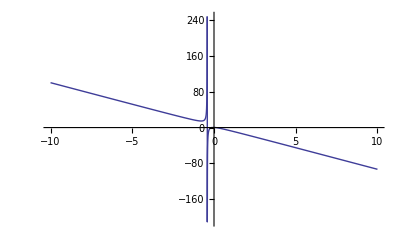

```mathematica
Plot[P2[[4]], {v,-10, 10}]
```